```mathematica
(* calulate effective potential for two opposite charges in various distances, by integrating energy density (en) of such field configurations, arXiv:2108.07896 *)
```

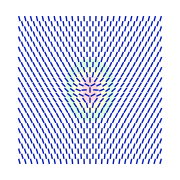
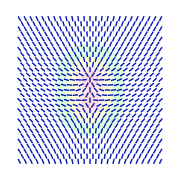
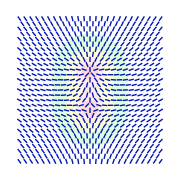
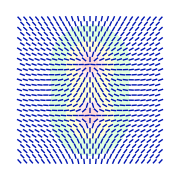
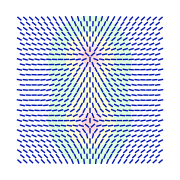
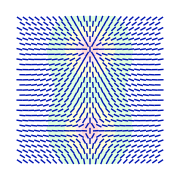

1589.56-25.1609/x

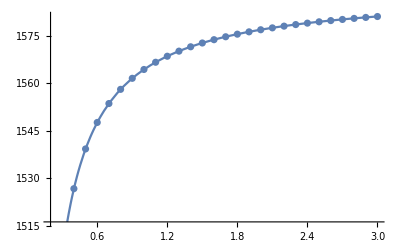

```mathematica
cos=1+(z-d)/Sqrt[(z-d)^2+r^2]-(z+d)/Sqrt[(z+d)^2+r^2];              (* Manfried Faber dipole ansatz *)
n={Sqrt[1-cos^2]x/r,Sqrt[1-cos^2]y/r,cos}/.r->Sqrt[x^2+y^2];                          (* vector field *)
M=KroneckerProduct[n,n];dM={D[M,x],D[M,y],D[M,z]};com[A_,B_]:=A.B-B.A;   (* ->matrix field*)
en=Simplify[Sum[Total[com[dM[[i]],dM[[j]]]^2,2],{i,2},{j,i+1,3}]];                          (*static Hamilitonian *)
Print[Row[Table[Show[Quiet[RegionPlot[{(en/.y->0)>1,(en/.y->0)>10,(en/.y->0)>100,(en/.y->0)>1000},
{x,-2,2},{z,-2,2},ImageSize->Small,Frame->False,PlotStyle->{LightGreen,LightYellow,LightPink,LightRed},BoundaryStyle->None]],
VectorPlot[n[[{1,3}]]/.y->0,{x,-2,2},{z,-2,2},VectorMarkers-> "Segment",VectorPoints->Fine]],{d,0.1,1.1,0.2}]]];      (* show configurations *)
enpm=Table[{d,Quiet[NIntegrate[4Pi*x(en/.{y->0})*Boole[x^2+(z-d)^2>0.001],   (* 0.001  cutoff *)
{x,0,Infinity},{z,0,Infinity}]]},{d,0.1,3,0.1}];                                         (* effective potential *)
Print[ftpm=Fit[enpm,{1,1/x},x]];                                                                                               (* fit Coulomb potential *)
Show[Plot[ftpm,{x,0.2,3}],ListPlot[enpm]]
```

```mathematica
(* find variation equation and verify that above ansatz satisfies it *)
```

```mathematica
cs=Cos[(α[z,r]+ϵ*η)];n={Sqrt[1-cs^2]x/r,Sqrt[1-cs^2]y/r,cs}/.r->Sqrt[x^2+y^2];
M=KroneckerProduct[n,n]/.η->η[x,y,z];dM={D[M,x],D[M,y],D[M,z]};
e=r*Simplify[Sum[Total[com[dM[[i]],dM[[j]]]^2,2],{i,2},{j,i+1,3}]/.{x->r,y->0},r>0];
var=Simplify[Coefficient[Series[e,{ϵ,0,1}],ϵ]];eq=FullSimplify[Coefficient[var,η[r,0,z]]-D[Coefficient[var,Derivative[1,0,0][η][r,0,z]],r]-D[Coefficient[var,Derivative[0,0,1][η][r,0,z]],z]]
```

-(4 Sin[α[z,r]] (r Cos[α[z,r]] ((α^(0,1)[z,r])^2+(α^(1,0)[z,r])^2)+Sin[α[z,r]] (-α^(0,1)[z,r]+r (α^(0,2)[z,r]+α^(2,0)[z,r]))))/r^2

```mathematica
eq/.{α[z,r]->ArcCos[cos],Derivative[1,0][α][z,r]->D[ArcCos[cos],z],Derivative[2,0][α][z,r]->D[ArcCos[cos],z,z],Derivative[0,1][α][z,r]->D[ArcCos[cos],r],Derivative[0,2][α][z,r]->D[ArcCos[cos],r,r]}//Simplify
```

0

```mathematica
(* two plus charges - getting energy reducing with distance as in Coulomb: repulsion *)
```

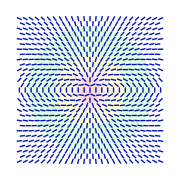
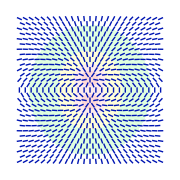
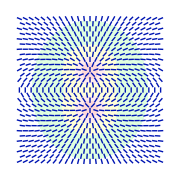
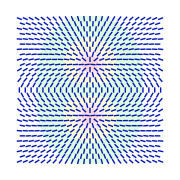
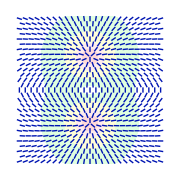
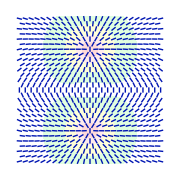

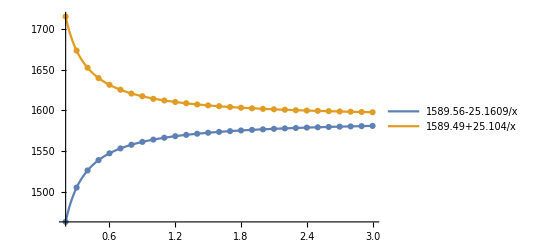

```mathematica
cos=(Mod[(z-d)/Sqrt[(z-d)^2+r^2]+(z+d)/Sqrt[(z+d)^2+r^2],2]-1);              (* plus-plus ansatz *)
n={Sqrt[1-cos^2]x/r,Sqrt[1-cos^2]y/r,cos}/.r->Sqrt[x^2+y^2];                          (* vector field *)
M=KroneckerProduct[n,n];dM={D[M,x],D[M,y],D[M,z]};com[A_,B_]:=A.B-B.A; (* ->matrix field*)
en=Simplify[Sum[Total[com[dM[[i]],dM[[j]]]^2,2],{i,2},{j,i+1,3}]];                          (*static Hamilitonian *)
Print[Row[Table[Show[Quiet[RegionPlot[{(en/.y->0)>1,(en/.y->0)>10,(en/.y->0)>100,(en/.y->0)>1000},
{x,-2,2},{z,-2,2},ImageSize->Small,Frame->False,PlotStyle->{LightGreen,LightYellow,LightPink,LightRed},BoundaryStyle->None]],
VectorPlot[n[[{1,3}]]/.y->0,{x,-2,2},{z,-2,2},VectorMarkers-> "Segment",VectorPoints->Fine]],{d,0.1,1.1,0.2}]]];      (* show configurations *)
enpp=Table[{d,Quiet[NIntegrate[4Pi*x(en/.{y->0})*Boole[x^2+(z-d)^2>0.001],   (* 0.001  cutoff *)
{x,0,Infinity},{z,0,Infinity}]]},{d,0.1,3,0.1}];                                         (* effective potential *)
ftpp=Fit[enpp,{1,1/x},x];                                                                                               (* fit Coulomb potential *)
Show[Plot[{ftpm,ftpp},{x,0.2,3},PlotLegends->{ftpm,ftpp}],ListPlot[{enpm,enpp}]]
```

```mathematica
(* simplified *)
```

```mathematica
cos=1+(z-d)/Sqrt[(z-d)^2+r^2]-(z+d)/Sqrt[(z+d)^2+r^2];   (*Manfried Faber dipole ansatz*)
n={Sqrt[1-cos^2]x/r,Sqrt[1-cos^2]y/r,cos}/.r->Sqrt[x^2+y^2];                       (* vector field *)
M=KroneckerProduct[n,n];dM={D[M,x],D[M,y],D[M,z]};com[A_,B_]:=A.B-B.A; (* ->matrix field*)
en=Simplify[Sum[Total[com[dM[[i]],dM[[j]]]^2,2],{i,2},{j,i+1,3}]];             (*static Hamilitonian *)
ens=Table[{d,NIntegrate[4Pi*x(en/.{y->0})*Boole[x^2+(z-d)^2>0.001],      (* 0.001  cutoff *)
{x,0,Infinity},{z,0,Infinity}]},{d,0.1,3,0.1}];                                      (* effective potential *)
Print[ft=Fit[ens,{1,1/x},x]]; Show[Plot[ft,{x,0.2,3}],ListPlot[ens]](*fit Coulomb potential*)
```